# Adopt a matrix

I imported the matrix from NIST matrix market. This matrix was generated using FIDAP package and used for Finite Element Modeling and it is 236 by 236 matrix.

```mathematica
A = Import["C:\\Users\\Dizzy\\Downloads\\e05r0000.mtx.gz"]
```

SparseArray[…]

```mathematica
SymmetricMatrixQ[A]
```

True

This matrix is a symmetric matrix as well as square matrix consisting of 236 rows and 236 columns.

```mathematica
MatrixPlot[A,PlotLegends->Automatic]
```

-Graphics-

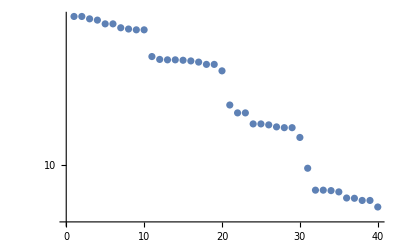

```mathematica
S = SingularValueList[A,40];
ListLogPlot[S]
```